Henry Osei

```mathematica
inearityCheck[g_,a_,MaxZoom_]:=Module[{x,f},f[x_]=g[x];
		DynamicModule[{Zoom= 1},
		Manipulate[Plot[f[x],{x,a-3/Zoom,a+3/Zoom},GridLines->Automatic,ImagePadding->15],
		{Zoom,0.5,MaxZoom}]]]
```

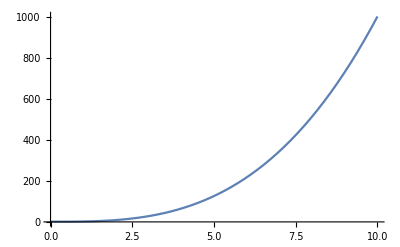

{1,1,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=x^3+1
Plot[f[x],{x,0,10}]
{Zoom,1,MaxZoom}
```

There is local linearity.

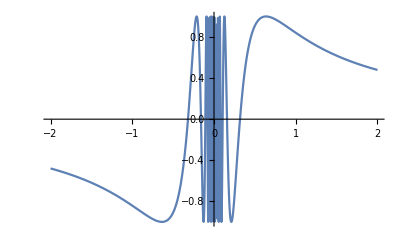

```mathematica
Clear [f,x]
f[x_]:=Sin[1/x]
Plot[f[x],{x,-2,2}]
{Zoom,0,MaxZoom}
```

```mathematica
{1,0,MaxZoom}
There is no local linearity.
```

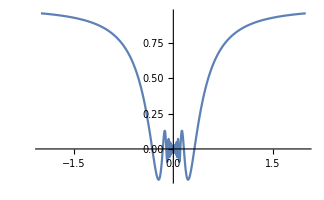

{1,0,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=x Sin[1/x]
Plot[f[x],{x,-2,2}]
{Zoom,0,MaxZoom}
```

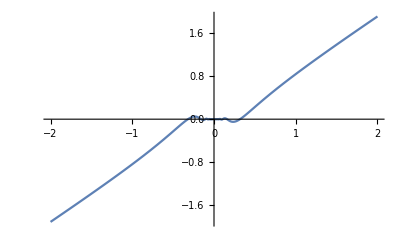

{1,0,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=x^2Sin[1/x]
Plot[f[x],{x,-2,2}]
{Zoom,0,MaxZoom}
There is local linearity.
```

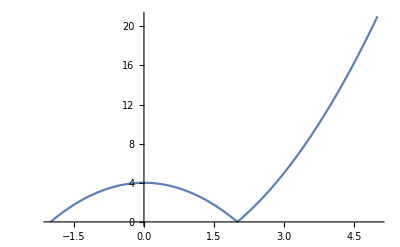

{1,2,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=Abs[x^2-4]
Plot[f[x],{x,-2,5}]
{Zoom,2,MaxZoom}
There is local linearity.
```

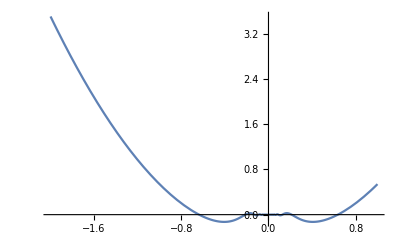

{1,0,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=x^2Cos[1/x]
Plot[f[x],{x,-2,1}]
{Zoom,0,MaxZoom}
There is no local linearity.
```

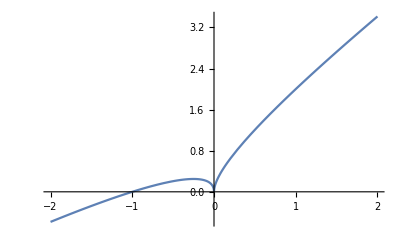

{1,-1,MaxZoom}

```mathematica
Clear [f,x]
f[x_]:=x+Sqrt[Abs[x]]
Plot[f[x],{x,-2,2}]
{Zoom,-1,MaxZoom}
There is local linearity.
```

```mathematica
Clear [f,x]
f[x_]:=x+Sqrt[Abs[x]]
Plot[f[x],{x,-2,2}]
{Zoom,0,MaxZoom}
There is no local linearity.
```

-Graphics-

```mathematica
{1,0,MaxZoom}
There is no local linearity.
```

```mathematica
secantLines[g_,a_]:=Module[{x,f},f[x_]=g[x];
DynamicModule[{b=a+1},
  {Manipulate[Plot[{f[x],If[b==a, 0,f[a]+(f[b]-f[a])/(b-a)*(x-a)]},{x,a-3,a+3},
 Epilog->{PointSize[Large],Point[{a,f[a]}], Point[Dynamic[{b,f[b]}]]} ],
   {{b,a+1},a-3,a+3},LocalizeVariables->False],
 Manipulate[Plot[f[x],{x,a-1.1*(b-a)-10^(-5),a+1.1*(b-a)+10^(-5)},
 GridLines->Automatic,ImagePadding->15,
 Epilog->{PointSize[Large],Point[{a,f[a]}], Point[Dynamic[{b,f[b]}]],
Red,Line[{{a,f[a]},Dynamic[{b,f[b]}]}]}
 ],{{b,a+1},a-3,a+3},LocalizeVariables->False]}
```

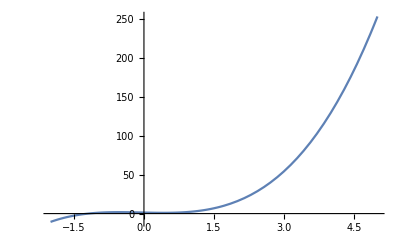

secantLines[f,2.2]

```mathematica
Clear [f,x]
f[x_]:=(x-2)^2/3+2x^3
Plot[f[x],{x,-2,5}]
secantLines[f,2.2]
```

```mathematica
D[secantLines[f,2.2], f]
```

secantLines^(1,0)[f,2.2]

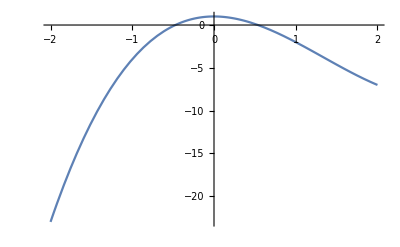

secantLines[f,1.3]

```mathematica
Clear [f,x]
f[x_]:=(x^3-4x^2+1)
Plot[f[x],{x,-2,2}]
secantLines[f,1.3]
```

```mathematica
D[secantLines[f,1.3], f]
```

secantLines^(1,0)[f,1.3]

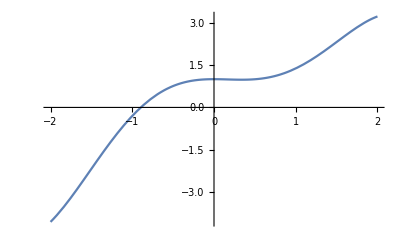

secantLines[f,1.8]

```mathematica
Clear [f,x]
f[x_]:=x^2Sin[x]+Cos[x]
Plot[f[x],{x,-2,2}]
secantLines[f,1.8]
```

```mathematica
D[secantLines[f,1.8], f]
```

secantLines^(1,0)[f,1.8]

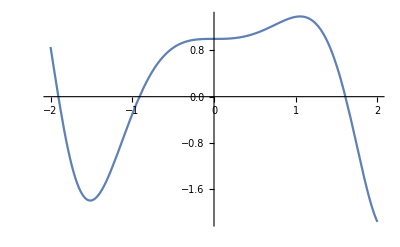

secantLines[f,1.2]

```mathematica
Clear [f,x]
f[x_]:=x Sin[x^2]+Cos[x^2]
Plot[f[x],{x,-2,2}]
secantLines[f,1.2]
```

```mathematica
D[secantLines[f,1.2], f]
```

secantLines^(1,0)[f,1.2]

The secant line joins two points of a function. The derivative of the function touches only one point.